## Объявление глобальных переменных

```mathematica
ClearAll["Global`*"]
grids[dist_]:=Table[If[OddQ@Round@(i/dist),{i,Dashed},{i}],{i,Ceiling@(#1/dist)*dist,Floor@(#2/dist)*dist,dist}]&;
Needs@"ErrorBarPlots`";
dropLastDot@string_:=If[StringTake[string,-1]===".",StringDrop[string,-1],string];
vertSize=0.01;horizSize=0.01;
vertCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1+vertSize,#2},{#1-vertSize,#2}}&@@@{coord1,coord2})};
horizCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1,#2+horizSize},{#1,#2-horizSize}}&@@@{coord1,coord2})};
```

## Построение одного графика

### Импорт табличных данных

```mathematica
dataN=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/42/tables/N.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataN//TableForm
```

N | I, A | dA, A | N | N-Nf | d(N-Nf) | p | dP | T | dT |  | 
1. | 0. | 0.02 | 0.66 | -0.13 | 0.14 | 0. | 0. | 0. | 0. | 0. | 0.
2. | 0.2 | 0.02 | 0.71 | -0.08 | 0.14 | 51. | 5. | 3. | 0. | 0. | 0.
3. | 0.4 | 0.02 | 0.91 | 0.12 | 0.15 | 103. | 5. | 10. | 1. | 3.322 | 0.118
4. | 0.6 | 0.02 | 0.89 | 0.1 | 0.14 | 154. | 5. | 23. | 1. | 1.651 | 0.118
5. | 0.8 | 0.02 | 0.96 | 0.17 | 0.15 | 206. | 5. | 40. | 1. | 1.398 | 0.118
6. | 1. | 0.02 | 1.37 | 0.58 | 0.16 | 257. | 5. | 61. | 1. | 1.848 | 0.118
7. | 1.2 | 0.02 | 1.78 | 0.99 | 0.17 | 309. | 6. | 86. | 2. | 1.835 | 0.118
8. | 1.4 | 0.02 | 2.4 | 1.61 | 0.19 | 360. | 6. | 114. | 2. | 1.858 | 0.118
9. | 1.7 | 0.02 | 3.52 | 2.73 | 0.22 | 437. | 6. | 161. | 2. | 1.808 | 0.081
10. | 2. | 0.02 | 3.96 | 3.17 | 0.23 | 514. | 6. | 214. | 3. | 1.527 | 0.062
11. | 2.3 | 0.02 | 3.97 | 3.18 | 0.23 | 591. | 7. | 271. | 3. | 1.24 | 0.049
12. | 2.6 | 0.02 | 4.05 | 3.26 | 0.23 | 668. | 7. | 330. | 3. | 1.045 | 0.04
13. | 2.9 | 0.02 | 3.56 | 2.77 | 0.22 | 746. | 7. | 393. | 4. | 0.817 | 0.034
14. | 3.2 | 0.02 | 2.57 | 1.78 | 0.19 | 823. | 8. | 457. | 4. | 0.565 | 0.032
15. | 3.3 | 0.02 | 2.27 | 1.48 | 0.19 | 848. | 8. | 479. | 5. | 0.492 | 0.032
16. | 3.4 | 0.02 | 1.42 | 0.63 | 0.16 | 874. | 8. | 502. | 5. | 0.307 | 0.04
17. | 3.6 | 0.02 | 1.3 | 0.51 | 0.16 | 926. | 8. | 546. | 5. | 0.254 | 0.04
18. | 3.7 | 0.02 | 1. | 0.21 | 0.15 | 951. | 9. | 569. | 5. | 0.156 | 0.055
19. | 3.8 | 0.02 | 1.14 | 0.35 | 0.15 | 977. | 9. | 592. | 5. | 0.194 | 0.043
20. | 3.85 | 0.02 | 1.71 | 0.92 | 0.17 | 990. | 9. | 603. | 5. | 0.308 | 0.029
21. | 3.9 | 0.02 | 2.89 | 2.1 | 0.2 | 1003. | 9. | 614. | 5. | 0.456 | 0.023
22. | 3.95 | 0.02 | 4.42 | 3.63 | 0.24 | 1015. | 9. | 626. | 6. | 0.589 | 0.021
23. | 4. | 0.02 | 5.23 | 4.44 | 0.25 | 1028. | 9. | 637. | 6. | 0.639 | 0.02
24. | 4.1 | 0.02 | 5.11 | 4.32 | 0.25 | 1054. | 9. | 660. | 6. | 0.607 | 0.019
25. | 4.2 | 0.02 | 4.58 | 3.79 | 0.24 | 1080. | 9. | 684. | 6. | 0.549 | 0.019
26. | 4.3 | 0.02 | 4.23 | 3.44 | 0.23 | 1105. | 10. | 707. | 6. | 0.505 | 0.018
27. | 4.33 | 0.02 | 3.38 | 2.59 | 0.21 | 1113. | 10. | 714. | 6. | 0.433 | 0.019
28. | 4.35 | 0.02 | 2.4 | 1.61 | 0.19 | 1118. | 10. | 719. | 6. | 0.339 | 0.02
29. | 4.4 | 0.02 | 2.12 | 1.33 | 0.18 | 1131. | 10. | 730. | 6. | 0.303 | 0.021
30. | 4.5 | 0.02 | 0.9 | 0.11 | 0.15 | 1157. | 10. | 754. | 6. | 0.084 | 0.056
31. | 4.6 | 0.02 | 0.56 | -0.23 | 0.13 | 1183. | 10. | 777. | 7. | 0. | 0.
32. | 4.8 | 0.02 | 0.54 | -0.25 | 0.13 | 1234. | 10. | 825. | 7. | 0. | 0.
33. | 5. | 0.02 | 0.32 | -0.47 | 0.12 | 1285. | 11. | 872. | 7. | 0. | 0.

### Фитирование табличных данных

В первый столбец “data” указывается величина по оси x, во второй – по y.

```mathematica
forFitN=Sort@dataN⟦2;;,{2,5,7}⟧; 
forFitNCr=dataN⟦2;;,6⟧;
model =a*Exp[-(x-b)^2/c^2]+d*x^2*(Max[(f-Sqrt[x^2+e]),0])^2+g;
modelm =a*Exp[-(x-b)^2/c^2]+d*x^2*(f-Sqrt[x^2+e])^2+g;
(*model1 =a*Exp[-(x-e*1.98)^2/c^2]+d*x^2*Max[(f-Sqrt[x^2+e^2])^2,0]+g;*)
(*model1 =a*Exp[-(x-e*1.98)^2/(2 c^2)]+d*x^2*Max[{(f-Sqrt[x^2+e^2])^2+g,0}];*)
```

```mathematica
(*fit1=NonlinearModelFit[forFitN⟦All,{1,2}⟧,{model1,-5<g<5},{{a,5},{c,0.3},{d,2},{f, 4.4},{e,2},{g,0}},x]*)
fit=NonlinearModelFit[forFitN⟦All,{1,2}⟧,{modelm,1<a<6,3<b<4.2,0<c<10, 0.21<d<5, 4<f<10,0<e<100},{{a,5},{b,3.9},{c,0.3},{d,2},{f, 4.4},{e,2},{g,-0.0}},x(*, MaxIterations->10000*)]
(*fitP=NonlinearModelFit[forFitN⟦All,{3,2}⟧,{modelm(*,-0.2<g<1,1<a<4.5,3<b<4.1,0<c<10, 0.19<d<5, 4<f<5,0<e<10, -5<g<5*)},{{a,4.5},{b,1000},{c,100},{d,3},{f, 4.4},{e,2},{g,-0.2}},x(*, MaxIterations->10000*)]*)
fit@"ParameterTable"
(*fitP@"ParameterTable"*)
(*Plot[fit["Function"]@x, {x, 0, 32}] *)
degOfFree=7;
χ=√(Total[(fit["FitResiduals"]/forFitNCr)^2]/(Length[forFitN]-degOfFree));
χ^2
```

NonlinearModelFit::ivar: 300000000 is not a valid variable.

NonlinearModelFit[{{0.,-0.13},{0.2,-0.08},{0.4,0.12},{0.6,0.1},{0.8,0.17},{1.,0.58},{1.2,0.99},{1.4,1.61},{1.7,2.73},{2.,3.17},{2.3,3.18},{2.6,3.26},{2.9,2.77},{3.2,1.78},{3.3,1.48},{3.4,0.63},{3.6,0.51},{3.7,0.21},{3.8,0.35},{3.85,0.92},{3.9,2.1},{3.95,3.63},{4.,4.44},{4.1,4.32},{4.2,3.79},{4.3,3.44},{4.33,2.59},{4.35,1.61},{4.4,1.33},{4.5,0.11},{4.6,-0.23},{4.8,-0.25},{5.,-0.47}},{{a ⅇ^(-(-b+x)^2/90000000000000000)+g+d x^2 (37.75-√(e+x^2))^2,a ⅇ^(-(-b+x)^2/90000000000000000)+g+d x^2 (14-√(e+x^2))^2},1<a<6,3<b<4.2,False,0.21<d<5,4<{37.75,14}<10,0<e<100},{{a,5},{b,3.9},{300000000,0.3},{d,2},{{37.75,14},4.4},{e,2},{g,0.}},x]

NonlinearModelFit[{{0.,-0.13},{0.2,-0.08},{0.4,0.12},{0.6,0.1},{0.8,0.17},{1.,0.58},{1.2,0.99},{1.4,1.61},{1.7,2.73},{2.,3.17},{2.3,3.18},{2.6,3.26},{2.9,2.77},{3.2,1.78},{3.3,1.48},{3.4,0.63},{3.6,0.51},{3.7,0.21},{3.8,0.35},{3.85,0.92},{3.9,2.1},{3.95,3.63},{4.,4.44},{4.1,4.32},{4.2,3.79},{4.3,3.44},{4.33,2.59},{4.35,1.61},{4.4,1.33},{4.5,0.11},{4.6,-0.23},{4.8,-0.25},{5.,-0.47}},{{a ⅇ^(-(-b+x)^2/90000000000000000)+g+d x^2 (37.75-√(e+x^2))^2,a ⅇ^(-(-b+x)^2/90000000000000000)+g+d x^2 (14-√(e+x^2))^2},1<a<6,3<b<4.2,False,0.21<d<5,4<{37.75,14}<10,0<e<100},{{a,5},{b,3.9},{300000000,0.3},{d,2},{{37.75,14},4.4},{e,2},{g,0.}},x][ParameterTable]

43.1717 (NonlinearModelFit[{{0.,-0.13},{0.2,-0.08},{0.4,0.12},{0.6,0.1},{0.8,0.17},{1.,0.58},{1.2,0.99},{1.4,1.61},{1.7,2.73},{2.,3.17},{2.3,3.18},{2.6,3.26},{2.9,2.77},{3.2,1.78},{3.3,1.48},{3.4,0.63},{3.6,0.51},{3.7,0.21},{3.8,0.35},{3.85,0.92},{3.9,2.1},{3.95,3.63},{4.,4.44},{4.1,4.32},{4.2,3.79},{4.3,3.44},{4.33,2.59},{4.35,1.61},{4.4,1.33},{4.5,0.11},{4.6,-0.23},{4.8,-0.25},{5.,-0.47}},{{a ⅇ^(-(-b+x)^2/90000000000000000)+g+d x^2 (37.75-√(e+x^2))^2,a ⅇ^(-(-b+x)^2/90000000000000000)+g+d x^2 (14-√(e+x^2))^2},1<a<6,3<b<4.2,False,0.21<d<5,4<{37.75,14}<10,0<e<100},{{a,5},{b,3.9},{300000000,0.3},{d,2},{{37.75,14},4.4},{e,2},{g,0.}},x][FitResiduals])^2

```mathematica
fit["BestFitParameters"]
```

{a→4.80213,b→4.11697,c→0.171005,d→1.10696,f→13.2912,e→145.844,g→-0.471867}

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicXN[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.5}]
```

```mathematica
myTicYN[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.5}]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

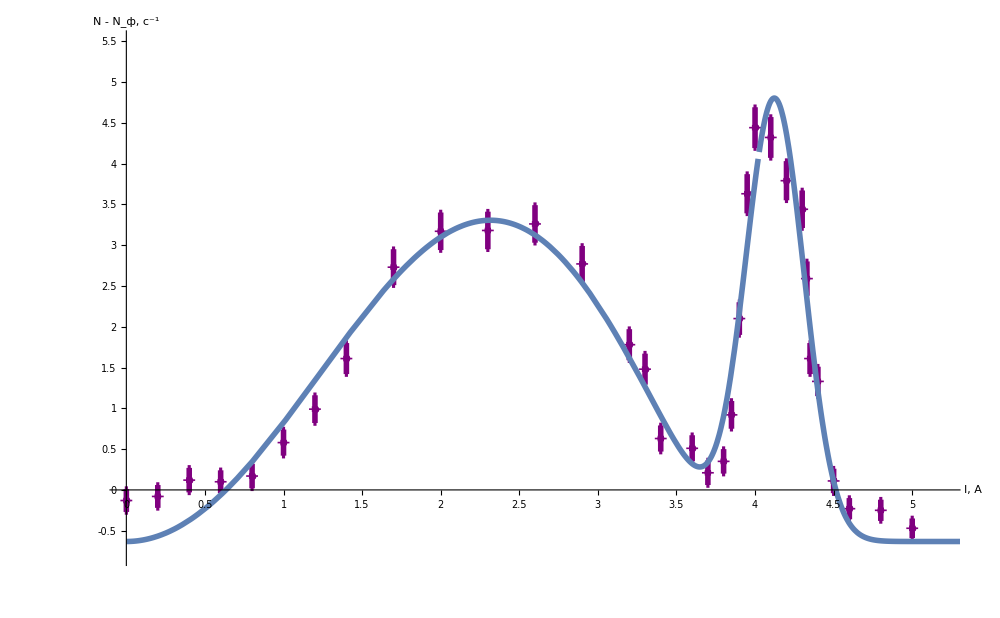

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataN⟦2;;,{2,5,3,6}⟧,
GridLines->{grids@0.25,grids@0.25},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"I, A","N - N_(:0444), (:0441)^-1"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.004,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
Ticks->{myTicXN,myTicYN},
PlotRange->{{0,5.2},{-0.8,5.5}}], 
Plot[fitm["Function"]@x,{x,0,10}, PlotStyle->Thickness@0.004]]
```

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeX=MapAt[dropLastDot@*ToString,dataN,{{2;;,All}}];
forTeX//TeXForm
```

\left(
\begin{array}{cccccccccccc}
 \text{N} & \text{I, A} & \text{dA, A} & \text{N} & \text{N-Nf} & \text{d(N-Nf)} & \text{p} & \text{dP} & \text{T} & \text{dT} & \text{} & \text{} \\
 1 & 0 & 0.02 & 0.66 & -0.13 & 0.14 & 0 & 0 & 0 & 0 & 0 & 0 \\
 2 & 0.2 & 0.02 & 0.71 & -0.08 & 0.14 & 51 & 5 & 3 & 0 & 0 & 0 \\
 3 & 0.4 & 0.02 & 0.91 & 0.12 & 0.15 & 103 & 5 & 10 & 1 & 3.322 & 0.118 \\
 4 & 0.6 & 0.02 & 0.89 & 0.1 & 0.14 & 154 & 5 & 23 & 1 & 1.651 & 0.118 \\
 5 & 0.8 & 0.02 & 0.96 & 0.17 & 0.15 & 206 & 5 & 40 & 1 & 1.398 & 0.118 \\
 6 & 1 & 0.02 & 1.37 & 0.58 & 0.16 & 257 & 5 & 61 & 1 & 1.848 & 0.118 \\
 7 & 1.2 & 0.02 & 1.78 & 0.99 & 0.17 & 309 & 6 & 86 & 2 & 1.835 & 0.118 \\
 8 & 1.4 & 0.02 & 2.4 & 1.61 & 0.19 & 360 & 6 & 114 & 2 & 1.858 & 0.118 \\
 9 & 1.7 & 0.02 & 3.52 & 2.73 & 0.22 & 437 & 6 & 161 & 2 & 1.808 & 0.081 \\
 10 & 2 & 0.02 & 3.96 & 3.17 & 0.23 & 514 & 6 & 214 & 3 & 1.527 & 0.062 \\
 11 & 2.3 & 0.02 & 3.97 & 3.18 & 0.23 & 591 & 7 & 271 & 3 & 1.24 & 0.049 \\
 12 & 2.6 & 0.02 & 4.05 & 3.26 & 0.23 & 668 & 7 & 330 & 3 & 1.045 & 0.04 \\
 13 & 2.9 & 0.02 & 3.56 & 2.77 & 0.22 & 746 & 7 & 393 & 4 & 0.817 & 0.034 \\
 14 & 3.2 & 0.02 & 2.57 & 1.78 & 0.19 & 823 & 8 & 457 & 4 & 0.565 & 0.032 \\
 15 & 3.3 & 0.02 & 2.27 & 1.48 & 0.19 & 848 & 8 & 479 & 5 & 0.492 & 0.032 \\
 16 & 3.4 & 0.02 & 1.42 & 0.63 & 0.16 & 874 & 8 & 502 & 5 & 0.307 & 0.04 \\
 17 & 3.6 & 0.02 & 1.3 & 0.51 & 0.16 & 926 & 8 & 546 & 5 & 0.254 & 0.04 \\
 18 & 3.7 & 0.02 & 1 & 0.21 & 0.15 & 951 & 9 & 569 & 5 & 0.156 & 0.055 \\
 19 & 3.8 & 0.02 & 1.14 & 0.35 & 0.15 & 977 & 9 & 592 & 5 & 0.194 & 0.043 \\
 20 & 3.85 & 0.02 & 1.71 & 0.92 & 0.17 & 990 & 9 & 603 & 5 & 0.308 & 0.029 \\
 21 & 3.9 & 0.02 & 2.89 & 2.1 & 0.2 & 1003 & 9 & 614 & 5 & 0.456 & 0.023 \\
 22 & 3.95 & 0.02 & 4.42 & 3.63 & 0.24 & 1015 & 9 & 626 & 6 & 0.589 & 0.021 \\
 23 & 4 & 0.02 & 5.23 & 4.44 & 0.25 & 1028 & 9 & 637 & 6 & 0.639 & 0.02 \\
 24 & 4.1 & 0.02 & 5.11 & 4.32 & 0.25 & 1054 & 9 & 660 & 6 & 0.607 & 0.019 \\
 25 & 4.2 & 0.02 & 4.58 & 3.79 & 0.24 & 1080 & 9 & 684 & 6 & 0.549 & 0.019 \\
 26 & 4.3 & 0.02 & 4.23 & 3.44 & 0.23 & 1105 & 10 & 707 & 6 & 0.505 & 0.018 \\
 27 & 4.33 & 0.02 & 3.38 & 2.59 & 0.21 & 1113 & 10 & 714 & 6 & 0.433 & 0.019 \\
 28 & 4.35 & 0.02 & 2.4 & 1.61 & 0.19 & 1118 & 10 & 719 & 6 & 0.339 & 0.02 \\
 29 & 4.4 & 0.02 & 2.12 & 1.33 & 0.18 & 1131 & 10 & 730 & 6 & 0.303 & 0.021 \\
 30 & 4.5 & 0.02 & 0.9 & 0.11 & 0.15 & 1157 & 10 & 754 & 6 & 0.084 & 0.056 \\
 31 & 4.6 & 0.02 & 0.56 & -0.23 & 0.13 & 1183 & 10 & 777 & 7 & 0 & 0 \\
 32 & 4.8 & 0.02 & 0.54 & -0.25 & 0.13 & 1234 & 10 & 825 & 7 & 0 & 0 \\
 33 & 5 & 0.02 & 0.32 & -0.47 & 0.12 & 1285 & 11 & 872 & 7 & 0 & 0 \\
\end{array}
\right)

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

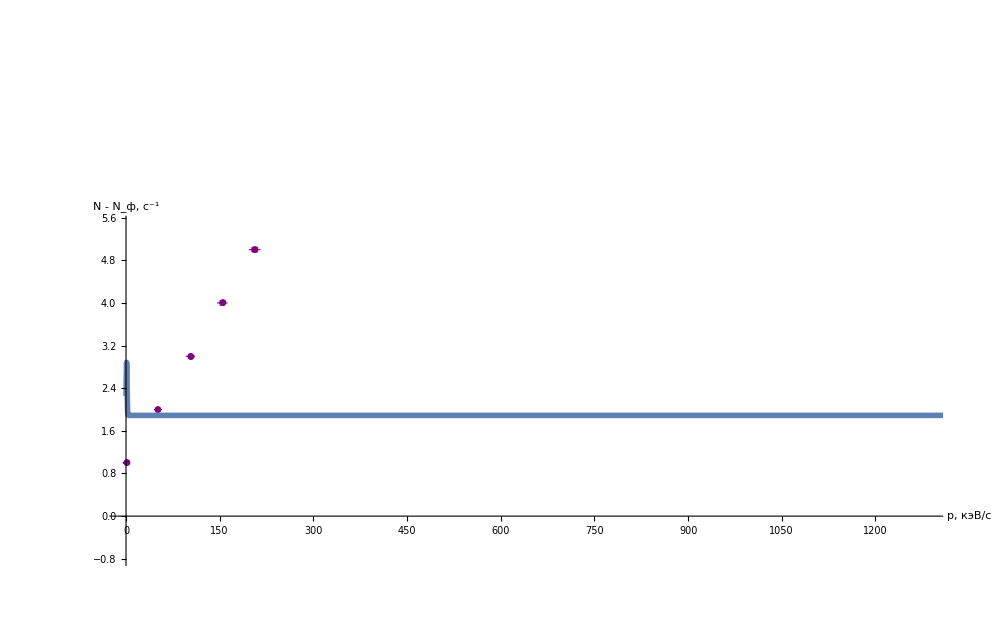

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataN⟦2;;,{7,1,1,3}⟧,
GridLines->{grids@1500,grids@1500},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"p, кэВ/c","N - N_(:0444), (:0441)^-1"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.004,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
(*Ticks->{myTicXN,myTicYN},*)
PlotRange->{{0,1282},{-0.8,5.5}}], 
Plot[fitP["Function"]@x,{x,0,1500}, PlotStyle->Thickness@0.004]]
```

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeX=MapAt[dropLastDot@*ToString,data,{{2;;,All}}];
forTeX//TeXForm
```

### Импорт табличных данных

```mathematica
dataK=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/42/tables/kir.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataK//TableForm
```

I | sigI | N | sigN | p | T | sigp | sigT
0.02 | 0.02 | 1.47 | 0.12 | 6. | 0.03 | 6. | 0.06
0.2 | 0.02 | 1.64 | 0.13 | 57. | 3.2 | 6. | 0.6
0.4 | 0.02 | 1.54 | 0.12 | 114. | 12.6 | 6. | 1.3
0.6 | 0.02 | 1.68 | 0.13 | 171. | 28. | 6. | 2.
0.8 | 0.02 | 1.93 | 0.14 | 228. | 49. | 6. | 3.
1. | 0.02 | 2.14 | 0.15 | 285. | 74. | 7. | 3.
1.1 | 0.02 | 2.8 | 0.2 | 314. | 89. | 7. | 4.
1.2 | 0.02 | 2.9 | 0.2 | 343. | 104. | 7. | 4.
1.4 | 0.02 | 3.2 | 0.2 | 400. | 138. | 7. | 4.
1.6 | 0.02 | 3.5 | 0.2 | 457. | 174. | 8. | 5.
1.8 | 0.02 | 3.6 | 0.2 | 514. | 214. | 8. | 6.
2. | 0.02 | 3.8 | 0.2 | 571. | 255. | 9. | 6.
2.2 | 0.02 | 3.9 | 0.2 | 628. | 299. | 9. | 7.
2.4 | 0.02 | 3.5 | 0.2 | 685. | 344. | 10. | 8.
2.6 | 0.02 | 3.1 | 0.2 | 742. | 390. | 10. | 8.
2.8 | 0.02 | 2.8 | 0.2 | 799. | 438. | 11. | 9.
3. | 0.02 | 2.5 | 0.2 | 856. | 486. | 11. | 10.
3.1 | 0.02 | 2.8 | 0.2 | 885. | 511. | 11. | 10.
3.2 | 0.02 | 2.7 | 0.2 | 914. | 536. | 12. | 10.
3.25 | 0.02 | 3.1 | 0.2 | 928. | 548. | 12. | 10.
3.3 | 0.02 | 3.6 | 0.2 | 942. | 561. | 12. | 11.
3.35 | 0.02 | 3.6 | 0.2 | 956. | 573. | 12. | 11.
3.4 | 0.02 | 4.1 | 0.2 | 971. | 586. | 12. | 11.
3.45 | 0.02 | 4. | 0.2 | 985. | 599. | 12. | 11.
3.5 | 0.02 | 4.6 | 0.2 | 999. | 611. | 13. | 11.
3.55 | 0.02 | 4.2 | 0.2 | 1013. | 624. | 13. | 11.
3.6 | 0.02 | 3.9 | 0.2 | 1028. | 637. | 13. | 11.
3.65 | 0.02 | 3.9 | 0.2 | 1042. | 650. | 13. | 12.
3.7 | 0.02 | 4.2 | 0.2 | 1056. | 662. | 13. | 12.
3.75 | 0.02 | 3.6 | 0.2 | 1071. | 675. | 13. | 12.
3.8 | 0.02 | 3.1 | 0.2 | 1085. | 688. | 13. | 12.
3.9 | 0.02 | 2.4 | 0.2 | 1113. | 714. | 14. | 12.
4. | 0.02 | 1.39 | 0.12 | 1142. | 740. | 14. | 13.
4.1 | 0.02 | 1.23 | 0.11 | 1170. | 766. | 14. | 13.
4.2 | 0.02 | 0.84 | 0.09 | 1199. | 792. | 15. | 13.
4.3 | 0.02 | 0.82 | 0.09 | 1228. | 819. | 15. | 14.
4.4 | 0.02 | 0.74 | 0.09 | 1256. | 845. | 15. | 14.

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeXkir=MapAt[dropLastDot@*ToString,dataK,{{2;;,All}}];
forTeXkir//TeXForm
```

\left(
\begin{array}{cccccccc}
 \text{I} & \text{sigI} & \text{N} & \text{sigN} & \text{p} & \text{T} & \text{sigp} & \text{sigT} \\
 0.02 & 0.02 & 1.47 & 0.12 & 6 & 0.03 & 6 & 0.06 \\
 0.2 & 0.02 & 1.64 & 0.13 & 57 & 3.2 & 6 & 0.6 \\
 0.4 & 0.02 & 1.54 & 0.12 & 114 & 12.6 & 6 & 1.3 \\
 0.6 & 0.02 & 1.68 & 0.13 & 171 & 28 & 6 & 2 \\
 0.8 & 0.02 & 1.93 & 0.14 & 228 & 49 & 6 & 3 \\
 1 & 0.02 & 2.14 & 0.15 & 285 & 74 & 7 & 3 \\
 1.1 & 0.02 & 2.8 & 0.2 & 314 & 89 & 7 & 4 \\
 1.2 & 0.02 & 2.9 & 0.2 & 343 & 104 & 7 & 4 \\
 1.4 & 0.02 & 3.2 & 0.2 & 400 & 138 & 7 & 4 \\
 1.6 & 0.02 & 3.5 & 0.2 & 457 & 174 & 8 & 5 \\
 1.8 & 0.02 & 3.6 & 0.2 & 514 & 214 & 8 & 6 \\
 2 & 0.02 & 3.8 & 0.2 & 571 & 255 & 9 & 6 \\
 2.2 & 0.02 & 3.9 & 0.2 & 628 & 299 & 9 & 7 \\
 2.4 & 0.02 & 3.5 & 0.2 & 685 & 344 & 10 & 8 \\
 2.6 & 0.02 & 3.1 & 0.2 & 742 & 390 & 10 & 8 \\
 2.8 & 0.02 & 2.8 & 0.2 & 799 & 438 & 11 & 9 \\
 3 & 0.02 & 2.5 & 0.2 & 856 & 486 & 11 & 10 \\
 3.1 & 0.02 & 2.8 & 0.2 & 885 & 511 & 11 & 10 \\
 3.2 & 0.02 & 2.7 & 0.2 & 914 & 536 & 12 & 10 \\
 3.25 & 0.02 & 3.1 & 0.2 & 928 & 548 & 12 & 10 \\
 3.3 & 0.02 & 3.6 & 0.2 & 942 & 561 & 12 & 11 \\
 3.35 & 0.02 & 3.6 & 0.2 & 956 & 573 & 12 & 11 \\
 3.4 & 0.02 & 4.1 & 0.2 & 971 & 586 & 12 & 11 \\
 3.45 & 0.02 & 4 & 0.2 & 985 & 599 & 12 & 11 \\
 3.5 & 0.02 & 4.6 & 0.2 & 999 & 611 & 13 & 11 \\
 3.55 & 0.02 & 4.2 & 0.2 & 1013 & 624 & 13 & 11 \\
 3.6 & 0.02 & 3.9 & 0.2 & 1028 & 637 & 13 & 11 \\
 3.65 & 0.02 & 3.9 & 0.2 & 1042 & 650 & 13 & 12 \\
 3.7 & 0.02 & 4.2 & 0.2 & 1056 & 662 & 13 & 12 \\
 3.75 & 0.02 & 3.6 & 0.2 & 1071 & 675 & 13 & 12 \\
 3.8 & 0.02 & 3.1 & 0.2 & 1085 & 688 & 13 & 12 \\
 3.9 & 0.02 & 2.4 & 0.2 & 1113 & 714 & 14 & 12 \\
 4 & 0.02 & 1.39 & 0.12 & 1142 & 740 & 14 & 13 \\
 4.1 & 0.02 & 1.23 & 0.11 & 1170 & 766 & 14 & 13 \\
 4.2 & 0.02 & 0.84 & 0.09 & 1199 & 792 & 15 & 13 \\
 4.3 & 0.02 & 0.82 & 0.09 & 1228 & 819 & 15 & 14 \\
 4.4 & 0.02 & 0.74 & 0.09 & 1256 & 845 & 15 & 14 \\
\end{array}
\right)

### Импорт табличных данных

```mathematica
dataNm=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/42/tables/Nm.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataNm//TableForm
```

5. | 0.8 | 0.02 | 0.96 | 0.17 | 0.15 | 207.
6. | 1. | 0.02 | 1.37 | 0.58 | 0.16 | 258.
7. | 1.2 | 0.02 | 1.78 | 0.99 | 0.17 | 310.
8. | 1.4 | 0.02 | 2.4 | 1.61 | 0.19 | 362.
9. | 1.7 | 0.02 | 3.52 | 2.73 | 0.22 | 439.
10. | 2. | 0.02 | 3.96 | 3.17 | 0.23 | 517.
11. | 2.3 | 0.02 | 3.97 | 3.18 | 0.23 | 594.
12. | 2.6 | 0.02 | 4.05 | 3.26 | 0.23 | 672.
13. | 2.9 | 0.02 | 3.56 | 2.77 | 0.22 | 749.
14. | 3.2 | 0.02 | 2.57 | 1.78 | 0.19 | 827.
15. | 3.3 | 0.02 | 2.27 | 1.48 | 0.19 | 853.
16. | 3.4 | 0.02 | 1.42 | 0.63 | 0.16 | 878.
17. | 3.6 | 0.02 | 1.3 | 0.51 | 0.16 | 930.
18. | 3.7 | 0.02 | 1. | 0.21 | 0.15 | 956.
19. | 3.8 | 0.02 | 1.14 | 0.35 | 0.15 | 982.
20. | 3.85 | 0.02 | 1.71 | 0.92 | 0.17 | 995.
21. | 3.9 | 0.02 | 2.89 | 2.1 | 0.2 | 1008.
22. | 3.95 | 0.02 | 4.42 | 3.63 | 0.24 | 1020.
23. | 4. | 0.02 | 5.23 | 4.44 | 0.25 | 1033.
24. | 4.1 | 0.02 | 5.11 | 4.32 | 0.25 | 1059.
25. | 4.2 | 0.02 | 4.58 | 3.79 | 0.24 | 1085.
26. | 4.3 | 0.02 | 4.23 | 3.44 | 0.23 | 1111.
27. | 4.33 | 0.02 | 3.38 | 2.59 | 0.21 | 1119.
28. | 4.35 | 0.02 | 2.4 | 1.61 | 0.19 | 1124.
29. | 4.4 | 0.02 | 2.12 | 1.33 | 0.18 | 1137.
30. | 4.5 | 0.02 | 0.9 | 0.11 | 0.15 | 1163.
31. | 4.6 | 0.02 | 0.56 | -0.23 | 0.13 | 1188.
32. | 4.8 | 0.02 | 0.54 | -0.25 | 0.13 | 1240.

```mathematica
forFitNm=Sort@dataNm⟦2;;,{2,5,7}⟧; 
forFitNCrm=dataNm⟦2;;,6⟧;
model =a*Exp[-(x-b)^2/(2 c^2)]+d*x^2*(Max[(f-Sqrt[x^2+e]),0])^2+g;
modelm =a*Exp[-(x-b)^2/c^2]+d*x^2*(f-Sqrt[x^2+e])^2+g;
(*model1 =a*Exp[-(x-e*1.98)^2/c^2]+d*x^2*Max[(f-Sqrt[x^2+e^2])^2,0]+g;*)
(*model1 =a*Exp[-(x-e*1.98)^2/(2 c^2)]+d*x^2*Max[{(f-Sqrt[x^2+e^2])^2+g,0}];*)
```

```mathematica
(*fit1=NonlinearModelFit[forFitN⟦All,{1,2}⟧,{model1,-5<g<5},{{a,5},{c,0.3},{d,2},{f, 4.4},{e,2},{g,0}},x]*)
fitm=NonlinearModelFit[forFitNm⟦All,{1,2}⟧,{model,1<a<6,3<b<4.2,0<c<10, 0.21<d<200, 4<f<20,0<e<500},{{a,5},{b,3.9},{c,0.3},{d,2},{f, 4.4},{e,2},{g,-0.0}},x(*, MaxIterations->2500*)]
fitP=NonlinearModelFit[forFitNm⟦All,{3,2}⟧,{model,-10<g<10(*,-0.2<g<1,1<a<4.5,3<b<4.1,0<c<10, 0.19<d<5, 4<f<5,0<e<10, -5<g<5*)},{a,b,c,d,f,e,g},x(*, MaxIterations->10000*)]
fitm@"ParameterTable"
fitP@"ParameterTable"
(*Plot[fit["Function"]@x, {x, 0, 32}] *)
degOfFree=7;
χm=√(Total[(fitm["FitResiduals"]/forFitNCrm)^2]/(Length[forFitNm]-degOfFree));
χm^2
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FittedModel[-0.632233+5.43501 ⅇ^(-14.0122 (-«18»+x)^2)+7.84971 x^2 Max[0,17.8458-√(302.287+x^2)]^2]

FittedModel[1.89074+1. ⅇ^(-0.5 (-1.+x)^2)+1. x^2 Max[0,1.-√(1.+x^2)]^2]

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a | 5.43501 | 0.362592 | 14.9893 | 2.43831×10^-12
b | 4.12248 | 0.0106437 | 387.317 | 3.12194×10^-40
c | 0.1889 | 0.0131098 | 14.4091 | 5.03781×10^-12
d | 7.84971 | 197.343 | 0.0397769 | 0.968665
f | 17.8458 | 218.38 | 0.0817188 | 0.935683
e | 302.287 | 7795.7 | 0.0387761 | 0.969453
g | -0.632233 | 0.274525 | -2.30301 | 0.0321464

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a | 1. | 0. | ∞ | 0.
b | 1. | 0. | ∞ | 0.
c | 1. | 9.13032551152651×10^-14339 | 1.09525120296922×10^14338 | 2.92431274692×10^-286749
d | 1. | 0. | ∞ | 0.
f | 1. | 0. | ∞ | 0.
e | 1. | 0. | ∞ | 0.
g | 1.89074 | 0.31531 | 5.99645 | 7.30034×10^-6

4.3713

```mathematica
dataNl=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/42/tables/Nl.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataNl//TableForm
```

11. | 2.3 | 0.02 | 3.97 | 3.18 | 0.23 | 591. | 7. | 271. | 3. | 1.24 | 0.049
12. | 2.6 | 0.02 | 4.05 | 3.26 | 0.23 | 668. | 7. | 330. | 3. | 1.045 | 0.04
13. | 2.9 | 0.02 | 3.56 | 2.77 | 0.22 | 746. | 7. | 393. | 4. | 0.817 | 0.034
14. | 3.2 | 0.02 | 2.57 | 1.78 | 0.19 | 823. | 8. | 457. | 4. | 0.565 | 0.032
15. | 3.3 | 0.02 | 2.27 | 1.48 | 0.19 | 848. | 8. | 479. | 5. | 0.492 | 0.032
16. | 3.4 | 0.02 | 1.42 | 0.63 | 0.16 | 874. | 8. | 502. | 5. | 0.307 | 0.04
17. | 3.6 | 0.02 | 1.3 | 0.51 | 0.16 | 926. | 8. | 546. | 5. | 0.254 | 0.04
18. | 3.7 | 0.02 | 1. | 0.21 | 0.15 | 951. | 9. | 569. | 5. | 0.156 | 0.055
19. | 3.8 | 0.02 | 1.14 | 0.35 | 0.15 | 977. | 9. | 592. | 5. | 0.194 | 0.043

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

```mathematica
forFitL=dataNl⟦2;;,{9,11}⟧;
forFit1CrL=dataNl⟦2;;,12⟧;
degOfFree=2;
fitL=Module[{x},LinearModelFit[forFitL,x^Range[0,degOfFree-1]//Evaluate,x]]
fitL@"ParameterTable"
Plot[fitL@x, {x, 0, 32}]
```

FittedModel[2.17334-0.00350484 x$350142]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 2.17334 | 0.126944 | 17.1205 | 2.54159×10^-6
x$350142 | -0.00350484 | 0.000258721 | -13.5468 | 0.0000100367

```mathematica
{{2.173339264595198, 0.12694403521222966}, {-0.003504838189441982, 0.00025872056756572027}}
```

{{2.17334,0.126944},{-0.00350484,0.000258721}}

```mathematica
TeXForm[{{2.173339264595198,0.12694403521222966},{-0.003504838189441982,0.00025872056756572027}}]
```

\left(
\begin{array}{cc}
 2.17334 & 0.126944 \\
 -0.00350484 & 0.000258721 \\
\end{array}
\right)

```mathematica
χ=√(Total[(fitL["FitResiduals"]/forFit1CrL)^2]/(Length[forFitL]-degOfFree));
χ^2
```

2.20119

```mathematica
fit1["FitResiduals"]
```

{0.015088,-0.010376,0.018466,-0.039528,-0.00782802,0.024178}

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

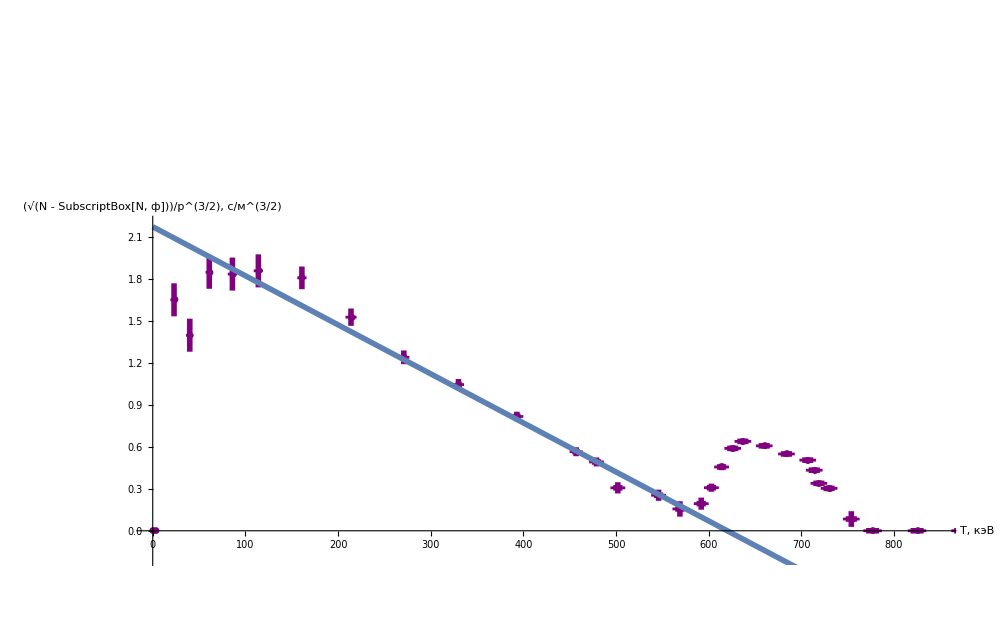

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataN⟦2;;,{9,11,10,12}⟧,
GridLines->{grids@25,grids@0.25},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"T, кэВ","(√(N  -  SubscriptBox[N, :0444]))/p^(3/2), (:0441)/(:043c)^(3/2)"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.004,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
(*Ticks->{myTicXN,myTicYN},*)
PlotRange->{{0,850},{-0.2,2.2}}], 
Plot[fitL["Function"]@x,{x,0,800}, PlotStyle->Thickness@0.004]]
```

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeX=MapAt[dropLastDot@*ToString,data,{{2;;,All}}];
forTeX//TeXForm
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

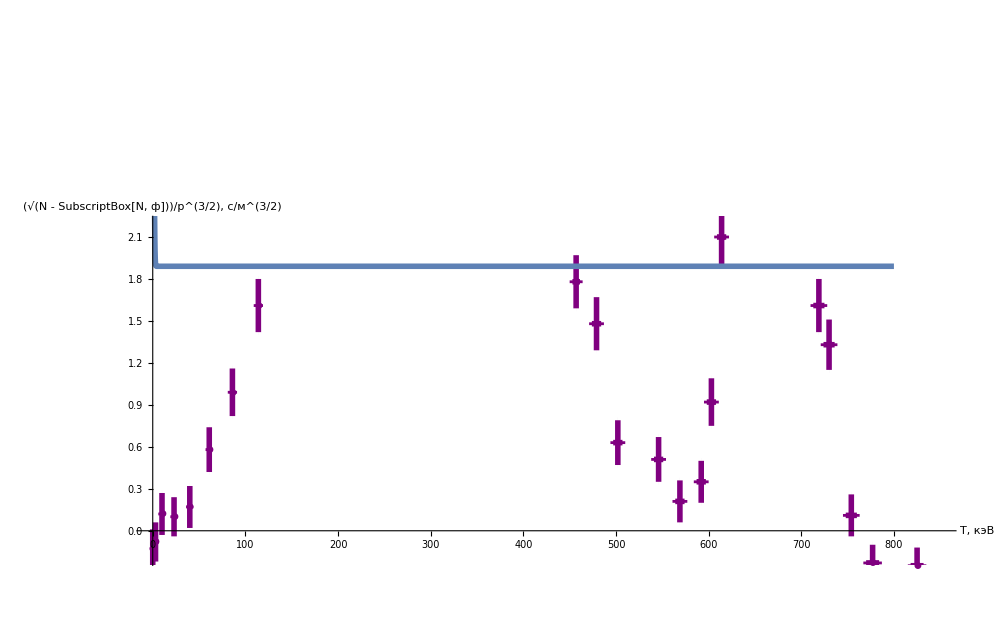

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataN⟦2;;,{9,5,10,6}⟧,
GridLines->{grids@25,grids@0.25},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"T, кэВ","(√(N  -  SubscriptBox[N, :0444]))/p^(3/2), (:0441)/(:043c)^(3/2)"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.004,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
(*Ticks->{myTicXN,myTicYN},*)
PlotRange->{{0,850},{-0.2,2.2}}], 
Plot[fitP["Function"]@x,{x,0,800}, PlotStyle->Thickness@0.004]]
```

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeX=MapAt[dropLastDot@*ToString,data,{{2;;,All}}];
forTeX//TeXForm
```

```mathematica
{{5.43502227962846, 0.3625923860932129}, {4.122483513208227, 0.010644123980589528}, {0.2671438828264804, 0.01854007714696791}, {7.8348801766868, 196.60219130372448}, {17.82942660153923, 217.76115004329623}, {301.70332576965137, 7766.483415822464}, {-0.6322381336408442, 0.27452818159683695}}
```

{{5.43502,0.362592},{4.12248,0.0106441},{0.267144,0.0185401},{7.83488,196.602},{17.8294,217.761},{301.703,7766.48},{-0.632238,0.274528}}

```mathematica
TeXForm[%1034]
```

\left(
\begin{array}{cc}
 5.43502 & 0.362592 \\
 4.12248 & 0.0106441 \\
 0.267144 & 0.0185401 \\
 7.83488 & 196.602 \\
 17.8294 & 217.761 \\
 301.703 & 7766.48 \\
 -0.632238 & 0.274528 \\
\end{array}
\right)

## Построение одного графика

### Импорт табличных данных

```mathematica
dataA=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/42/tables/ars.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataA//TableForm
```

Ia | N, 1/c | dI | dN
0. | -0.1 | 0.02 | 0.2
0.2 | -0.1 | 0.03 | 0.2
0.4 | -0.2 | 0.04 | 0.2
0.6 | -0.2 | 0.05 | 0.2
0.8 | 0.1 | 0.06 | 0.2
1. | 0.3 | 0.07 | 0.3
1.2 | 0.9 | 0.08 | 0.3
1.4 | 1.7 | 0.09 | 0.3
1.6 | 2.3 | 0.10 | 0.3
1.8 | 2.9 | 0.11 | 0.3
2. | 3. | 0.12 | 0.3
2.2 | 3.8 | 0.13 | 0.4
2.4 | 3.3 | 0.14 | 0.3
2.6 | 3.3 | 0.15 | 0.3
2.8 | 3.2 | 0.16 | 0.3
3. | 2.3 | 0.17 | 0.3
3.2 | 1.5 | 0.18 | 0.3
3.4 | 0.7 | 0.19 | 0.3
3.6 | 0.1 | 0.20 | 0.2
3.8 | 0.3 | 0.21 | 0.2
4. | 4.1 | 0.22 | 0.4
4.2 | 4.1 | 0.23 | 0.4
4.4 | 1.2 | 0.24 | 0.3
4.6 | -0.2 | 0.25 | 0.2
4.8 | -0.3 | 0.26 | 0.2
5. | -0.5 | 0.27 | 0.2
3.9 | 1.6 | 0.28 | 0.3
4.1 | 4.8 | 0.29 | 0.4
4.3 | 3.3 | 0.30 | 0.3
4.5 | 0. | 0.31 | 0.2

### Фитирование табличных данных

В первый столбец “data” указывается величина по оси x, во второй – по y.

```mathematica
forFitA=Sort@dataA⟦2;;,{1,2,4}⟧; 
(*forFitNCr=dataN⟦2;;,6⟧;*)
model =a*Exp[-(x-b)^2/c^2]+d*x^2*(Max[(f-Sqrt[x^2+e]),0])^2+g;
modelm =a*Exp[-(x-b)^2/c^2]+d*x^2*(f-Sqrt[x^2+e])^2+g;
(*model1 =a*Exp[-(x-e*1.98)^2/c^2]+d*x^2*Max[(f-Sqrt[x^2+e^2])^2,0]+g;*)
(*model1 =a*Exp[-(x-e*1.98)^2/(2 c^2)]+d*x^2*Max[{(f-Sqrt[x^2+e^2])^2+g,0}];*)
```

```mathematica
(*fit1=NonlinearModelFit[forFitN⟦All,{1,2}⟧,{model1,-5<g<5},{{a,5},{c,0.3},{d,2},{f, 4.4},{e,2},{g,0}},x]*)
fitA=NonlinearModelFit[forFitA⟦All,{1,2}⟧,{model,1<a<6,3<b<4.2,0<c<10, 0.21<d<5, 4<f<10,0<e<100},{{a,5},{b,3.9},{c,0.3},{d,2},{f, 4.4},{e,2},{g,-0.0}},x(*, MaxIterations->10000*)]
(*fitP=NonlinearModelFit[forFitN⟦All,{3,2}⟧,{modelm(*,-0.2<g<1,1<a<4.5,3<b<4.1,0<c<10, 0.19<d<5, 4<f<5,0<e<10, -5<g<5*)},{{a,4.5},{b,1000},{c,100},{d,3},{f, 4.4},{e,2},{g,-0.2}},x(*, MaxIterations->10000*)]*)
fitA@"ParameterTable"
(*fitP@"ParameterTable"*)
(*Plot[fit["Function"]@x, {x, 0, 32}] *)
(*degOfFree=7;
χ=√(Total[(fit["FitResiduals"]/forFitA)^2]/(Length[forFitA]-degOfFree));
χ^2*)
```

FittedModel[-0.578066+5.51146 ⅇ^(-15.9144 (-«18»+x)^2)+2.36678 x^2 Max[0,9.99946-√(83.8482+x^2)]^2]

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a | 5.51146 | 0.266652 | 20.6691 | 2.35721×10^-16
b | 4.13292 | 0.00967436 | 427.204 | 2.34972×10^-46
c | 0.250672 | 0.0148636 | 16.8648 | 1.91766×10^-14
d | 2.36678 | 13.0489 | 0.181378 | 0.85766
f | 9.99946 | 25.09 | 0.398543 | 0.693905
e | 83.8482 | 502.818 | 0.166757 | 0.869019
g | -0.578066 | 0.132193 | -4.37289 | 0.000222264

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicXN[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.5}]
```

```mathematica
myTicYN[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.5}]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

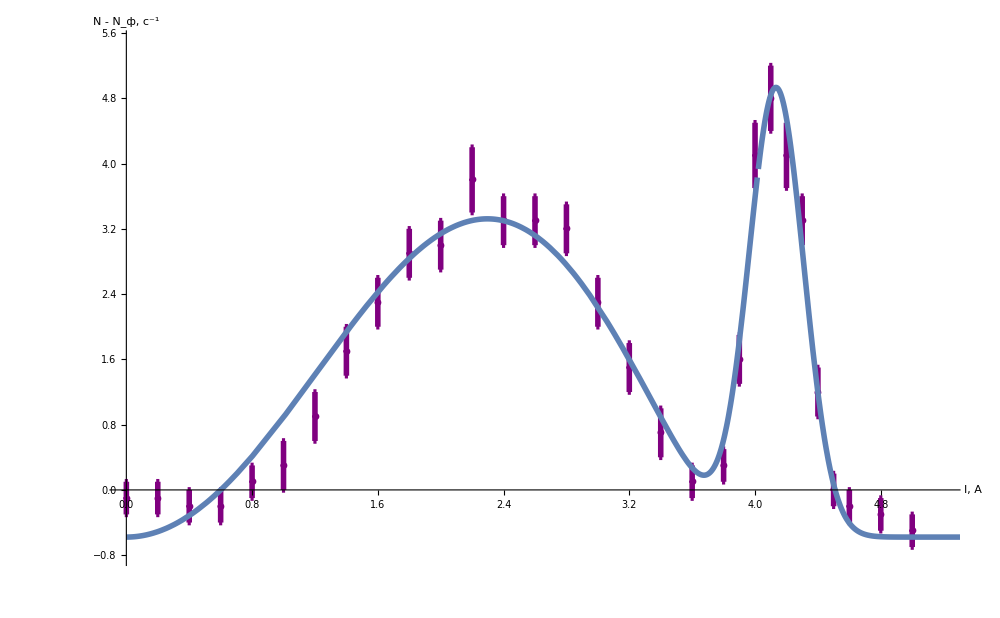

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataA⟦2;;,{1,2,3,4}⟧,
GridLines->{grids@0.25,grids@0.25},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"I, A","N - N_(:0444), (:0441)^-1"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.004,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
(*Ticks->{myTicXN,myTicYN},*)
PlotRange->{{0,5.2},{-0.8,5.5}}], 
Plot[fitA["Function"]@x,{x,0,10}, PlotStyle->Thickness@0.004]]
```

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeX=MapAt[dropLastDot@*ToString,dataN,{{2;;,All}}];
forTeX//TeXForm
```

\left(
\begin{array}{cccccccccccc}
 \text{N} & \text{I, A} & \text{dA, A} & \text{N} & \text{N-Nf} & \text{d(N-Nf)} & \text{p} & \text{dP} & \text{T} & \text{dT} & \text{} & \text{} \\
 1 & 0 & 0.02 & 0.66 & -0.13 & 0.14 & 0 & 0 & 0 & 0 & 0 & 0 \\
 2 & 0.2 & 0.02 & 0.71 & -0.08 & 0.14 & 51 & 5 & 3 & 0 & 0 & 0 \\
 3 & 0.4 & 0.02 & 0.91 & 0.12 & 0.15 & 103 & 5 & 10 & 1 & 3.322 & 0.118 \\
 4 & 0.6 & 0.02 & 0.89 & 0.1 & 0.14 & 154 & 5 & 23 & 1 & 1.651 & 0.118 \\
 5 & 0.8 & 0.02 & 0.96 & 0.17 & 0.15 & 206 & 5 & 40 & 1 & 1.398 & 0.118 \\
 6 & 1 & 0.02 & 1.37 & 0.58 & 0.16 & 257 & 5 & 61 & 1 & 1.848 & 0.118 \\
 7 & 1.2 & 0.02 & 1.78 & 0.99 & 0.17 & 309 & 6 & 86 & 2 & 1.835 & 0.118 \\
 8 & 1.4 & 0.02 & 2.4 & 1.61 & 0.19 & 360 & 6 & 114 & 2 & 1.858 & 0.118 \\
 9 & 1.7 & 0.02 & 3.52 & 2.73 & 0.22 & 437 & 6 & 161 & 2 & 1.808 & 0.081 \\
 10 & 2 & 0.02 & 3.96 & 3.17 & 0.23 & 514 & 6 & 214 & 3 & 1.527 & 0.062 \\
 11 & 2.3 & 0.02 & 3.97 & 3.18 & 0.23 & 591 & 7 & 271 & 3 & 1.24 & 0.049 \\
 12 & 2.6 & 0.02 & 4.05 & 3.26 & 0.23 & 668 & 7 & 330 & 3 & 1.045 & 0.04 \\
 13 & 2.9 & 0.02 & 3.56 & 2.77 & 0.22 & 746 & 7 & 393 & 4 & 0.817 & 0.034 \\
 14 & 3.2 & 0.02 & 2.57 & 1.78 & 0.19 & 823 & 8 & 457 & 4 & 0.565 & 0.032 \\
 15 & 3.3 & 0.02 & 2.27 & 1.48 & 0.19 & 848 & 8 & 479 & 5 & 0.492 & 0.032 \\
 16 & 3.4 & 0.02 & 1.42 & 0.63 & 0.16 & 874 & 8 & 502 & 5 & 0.307 & 0.04 \\
 17 & 3.6 & 0.02 & 1.3 & 0.51 & 0.16 & 926 & 8 & 546 & 5 & 0.254 & 0.04 \\
 18 & 3.7 & 0.02 & 1 & 0.21 & 0.15 & 951 & 9 & 569 & 5 & 0.156 & 0.055 \\
 19 & 3.8 & 0.02 & 1.14 & 0.35 & 0.15 & 977 & 9 & 592 & 5 & 0.194 & 0.043 \\
 20 & 3.85 & 0.02 & 1.71 & 0.92 & 0.17 & 990 & 9 & 603 & 5 & 0.308 & 0.029 \\
 21 & 3.9 & 0.02 & 2.89 & 2.1 & 0.2 & 1003 & 9 & 614 & 5 & 0.456 & 0.023 \\
 22 & 3.95 & 0.02 & 4.42 & 3.63 & 0.24 & 1015 & 9 & 626 & 6 & 0.589 & 0.021 \\
 23 & 4 & 0.02 & 5.23 & 4.44 & 0.25 & 1028 & 9 & 637 & 6 & 0.639 & 0.02 \\
 24 & 4.1 & 0.02 & 5.11 & 4.32 & 0.25 & 1054 & 9 & 660 & 6 & 0.607 & 0.019 \\
 25 & 4.2 & 0.02 & 4.58 & 3.79 & 0.24 & 1080 & 9 & 684 & 6 & 0.549 & 0.019 \\
 26 & 4.3 & 0.02 & 4.23 & 3.44 & 0.23 & 1105 & 10 & 707 & 6 & 0.505 & 0.018 \\
 27 & 4.33 & 0.02 & 3.38 & 2.59 & 0.21 & 1113 & 10 & 714 & 6 & 0.433 & 0.019 \\
 28 & 4.35 & 0.02 & 2.4 & 1.61 & 0.19 & 1118 & 10 & 719 & 6 & 0.339 & 0.02 \\
 29 & 4.4 & 0.02 & 2.12 & 1.33 & 0.18 & 1131 & 10 & 730 & 6 & 0.303 & 0.021 \\
 30 & 4.5 & 0.02 & 0.9 & 0.11 & 0.15 & 1157 & 10 & 754 & 6 & 0.084 & 0.056 \\
 31 & 4.6 & 0.02 & 0.56 & -0.23 & 0.13 & 1183 & 10 & 777 & 7 & 0 & 0 \\
 32 & 4.8 & 0.02 & 0.54 & -0.25 & 0.13 & 1234 & 10 & 825 & 7 & 0 & 0 \\
 33 & 5 & 0.02 & 0.32 & -0.47 & 0.12 & 1285 & 11 & 872 & 7 & 0 & 0 \\
\end{array}
\right)